```mathematica
SetDirectory@NotebookDirectory[]
<<"MagnetCode`"
```

/Users/will/magcode/mathematica

## Setup

```mathematica
mm:=0.001
tesla:=1
amps:=1
ohms:=1

magnet={
MagnetRadius->5mm,
MagnetLength->10mm,
Magnetisation->1 tesla
}
coil={
CoilRadius->7mm,
CoilLength->20mm,
Current->1 amps,
WireRadius->0.1mm,
WireCoating->0.01mm,
CoilResistance->8ohms
}
CalculateCoilParams[parameters__] := 
  ReleaseHold[{
               Hold@Symbol["CoilRadius"]->CoilRadius,
               Hold@Symbol["CoilThickness"]->CoilThickness,
               Hold@Symbol["CoilTurns"]->TotalTurns,
               Hold@Symbol["CoilLength"]->CoilLength,
               Hold@Symbol["Current"]->Current
              } //. 
  Flatten@{{
    CoilThickness -> ( 2 WireLength (WireRadius+WireCoating)^2 ) /
                                (  π CoilLength (CoilRadius+WireRadius+WireCoating) ) ,
    WireLength -> CoilResistance WireArea / WireResistivity ,
    WireResistivity -> 1.7*10^-8, (* copper *)
    WireArea -> π (WireRadius+WireCoating)^2,
    TotalTurns -> TurnsZ TurnsR,
    TurnsZ -> Round[CoilLength / (2WireRadius+2WireCoating)],
    TurnsR -> Round[CoilThickness / (2WireRadius+2WireCoating)]
    },parameters}//.{cm->0.01,mm->0.001,volts->1,ohms->1}]

CalculateCoilParams[coil]
```

{MagnetRadius→0.005,MagnetLength→0.01,Magnetisation→1}

{CoilRadius→0.007,CoilLength→0.02,Current→1,WireRadius→0.0001,WireCoating→0.00001,CoilResistance→8}

{CoilRadius→0.007,CoilThickness→0.000969041,CoilTurns→364,CoilLength→0.02,Current→1}

## Comparison between different methods

Here we hope that a zero-thickness coil and a thin-thickness coil gives similar results.
Eccentricity should result in only small changes in force.

```mathematica
thinvthickparams={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilLength->20mm,
CoilTurns->400,
Current->1,

Displacement->10mm,
IntegrationPrecision->3
};
```

```mathematica
Print["Zero thickness coil:"]
Timing@MagnetCoilForce@{thinvthickparams}

Print["Low thickness coil: (two numerical integrals; two orders of magnitude slower)"]
Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.1mm
}

Print["Low thickness coil with small eccentricity: (three numerical integrals)"]
Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.1mm,
Eccentricity->0.1mm
}
```

Zero thickness coil:

{0.000527,-2.60128}

Low thickness coil: (two numerical integrals; two orders of magnitude slower)

{0.018072,-2.58613}

Low thickness coil with small eccentricity: (three numerical integrals)

{0.188145,2.53076}

## Comparison with the filament model

### Thin coil

```mathematica
filamentparams={

MagnetRadius->9mm,
MagnetLength->10mm,

(* Turn the magnet into a coil: *)
Magnetisation->1,
MagnetCurrent->Magnetisation MagnetLength/(4π 10^(-7) CoilTurns),

CoilRadius->10mm,
CoilLength->20mm,

CoilTurns->100,
Current->1

};
```

```mathematica
FilamentForce[r_,R_,z_]=z (1/(√((r+R)^2+z^2)) EllipticK[(4 r R)/((r+R)^2+z^2)]-(r^2+R^2+z^2)/(((r-R)^2+z^2) √((r+R)^2+z^2)) EllipticE[(4 r R)/((r+R)^2+z^2)]);
```

```mathematica
ThinCoilForceFilaments[pp__]:=Hold[Module[
{f1,f2},

f1=Table[-CoilLength/2+(n-1) CoilLength/(CoilTurns-1),{n,1,CoilTurns}];
f2=Table[-MagnetLength/2+(n-1) MagnetLength/(CoilTurns-1),{n,1,CoilTurns}];


4π 10^(-7)Current MagnetCurrent Sum[
FilamentForce[CoilRadius,MagnetRadius,Displacement+z1+z2]
,{z1,f1},{z2,f2}
]
]]//.pp//ReleaseHold
```

```mathematica
ThinCoilForceFilaments@Flatten@{Displacement->10mm,filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,CoilThickness->0.1mm,filamentparams}//.filamentparams
```

-0.641207

-0.650321

-0.646527

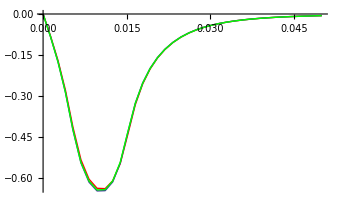

```mathematica
Show@{
Plot[(ThinCoilForceFilaments@Flatten@{Displacement->x,filamentparams}),{x,0,50mm},PlotPoints->10,MaxRecursion->2,PlotStyle->Red],
Plot[(MagnetCoilForce@Flatten@{Displacement->x,filamentparams})//.filamentparams,{x,0,50mm},PlotPoints->10,MaxRecursion->2],
Plot[(MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->0.1mm,filamentparams})//.filamentparams,{x,0,50mm},PlotPoints->10,MaxRecursion->2,PlotStyle->Green]
}
```

### Thick coil

```mathematica
thickfilamentparams:={

Displacement->10mm,
MagnetRadius->9mm,
MagnetLength->10mm,

(* Turn the magnet into a coil: *)
MagnetCurrent->Magnetisation MagnetLength/(4π 10^(-7) CoilTurns),
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurns->CoilTurnsR CoilTurnsZ,
CoilTurnsR->5,
CoilTurnsZ->20,
Current->1

}
```

```mathematica
ThickCoilForceFilaments[pp__]:=Hold[Module[
{fr,f1,f2},

fr=CoilRadius+Table[(n-1) (CoilThickness)/(CoilTurnsR-1),{n,1,CoilTurnsR}];
f1=Table[-CoilLength/2+(n-1) CoilLength/(CoilTurnsZ-1),{n,1,CoilTurnsZ}];
f2=Table[-MagnetLength/2+(n-1) MagnetLength/(CoilTurns-1),{n,1,CoilTurns }];

4π 10^(-7)Current MagnetCurrent Sum[
FilamentForce[rr,MagnetRadius,Displacement+z1+z2]
,{rr,fr},{z1,f1},{z2,f2}
]
]]//.pp//ReleaseHold

ThickCoilForceShell[pp__]:=(Hold[Module[{fr},
fr=CoilRadius+
(Hold@Table[(n-1) (CoilThickness)/(CoilTurnsR-1),{n,1,CoilTurnsR}]//.pp)//ReleaseHold;
 Sum[
MagnetCoilForce@Flatten@{CoilRadius->(rr//.pp),CoilThickness->0,pp}
,{rr,fr}
]/(CoilTurnsR//.pp)
]]//ReleaseHold)//.pp
```

```mathematica
Print["Zero coil thickness: (filament, shell)"]
Timing@ThinCoilForceFilaments@Flatten@{thickfilamentparams}
Timing@MagnetCoilForce@Flatten@{CoilThickness->0mm,thickfilamentparams}//.thickfilamentparams

Print["Non-zero coil thickness: (filament, shell, integral)"]
Timing@ThickCoilForceFilaments@thickfilamentparams
Timing@ThickCoilForceShell@thickfilamentparams
Timing@MagnetCoilForce@thickfilamentparams//.thickfilamentparams
```

Zero coil thickness: (filament, shell)

{0.372,-0.641207}

{0.000607,-0.650321}

Non-zero coil thickness: (filament, shell, integral)

{0.372291,-0.473645}

{0.002607,-0.497669}

{0.013308,-0.49944}

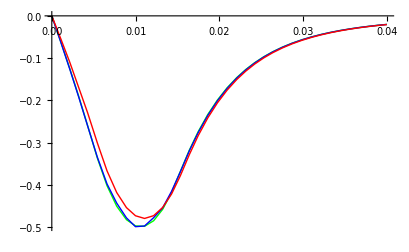

```mathematica
xmax:=40mm
Show@{
Plot[(ThickCoilForceShell[Flatten@{Displacement->x,thickfilamentparams}]),{x,0,xmax},PlotPoints->10,MaxRecursion->2,PlotStyle->Green],
Plot[(MagnetCoilForce[Flatten@{Displacement->x,thickfilamentparams}]//.thickfilamentparams),{x,0,xmax},PlotPoints->10,MaxRecursion->2,PlotStyle->Blue],
Plot[(ThickCoilForceFilaments[Flatten@{Displacement->x,thickfilamentparams}]),{x,0,xmax},PlotPoints->10,MaxRecursion->2,PlotStyle->Red]
}
```

Looks good!?

## Eccentricity

```mathematica
param={
MagnetRadius->5 mm,
MagnetLength->10 mm,
Magnetisation->1,
CalculateCoilParams@{
CoilRadius ->7 mm,
CoilLength-> 10mm,  
Current->3amps,
WireRadius->0.1mm,
WireCoating->0mm,
CoilResistance->8ohms
},
IntegrationPrecision->3
};
```

```mathematica
{Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->0mm}],{x,0mm,30mm}],
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->0.1mm}],{x,0mm,30mm}]}
```

$Aborted

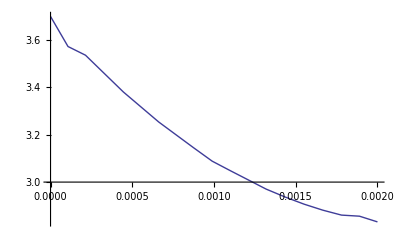

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->7.5mm,Eccentricity->x }],{x,0mm,2mm},MaxRecursion->1,PlotPoints->10]
```

Old:

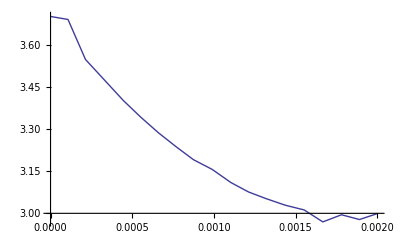

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->7.5mm,Eccentricity->x }],{x,0mm,2mm},MaxRecursion->1,PlotPoints->10]
```